```mathematica
1-(CDF[NormalDistribution[]][1.])^5
```

0.57843

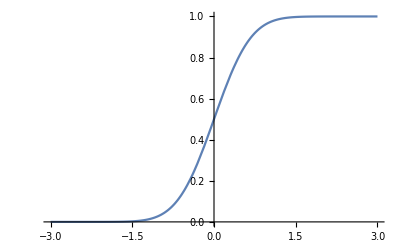

```mathematica
Plot[1-CDF[BinomialDistribution[5,1-CDF[NormalDistribution[x,1]][0]]][2],{x,-3,3}]
```

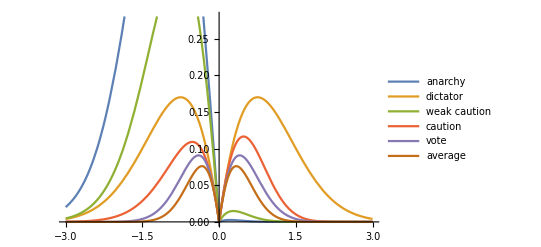

```mathematica
Plot[{Max[0,x]-(1-(CDF[NormalDistribution[x,1]][0])^5)x,(*anarchy*)
Max[0,x]-(1-(CDF[NormalDistribution[x,1]][0])^1)x,(*dictator*)
Max[0,x]-(1-(CDF[NormalDistribution[x,1]][.42])^5)x,(*weak caution = dictator*)
Max[0,x]-(1-(CDF[NormalDistribution[x,1]][1.165])^5)x,(*caution*)
Max[0,x]-(1-CDF[BinomialDistribution[5,1-CDF[NormalDistribution[x,1]][0]]][2])x,(*vote*)
Max[0,x]-(1-(CDF[NormalDistribution[x,1/Sqrt[5]]][0])^1)x(*average*)
},{x,-3,3},PlotLegends->{"anarchy","dictator","weak caution","caution","vote","average"}]
```

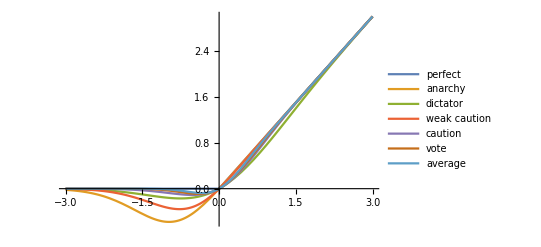

```mathematica
Plot[{Max[0,x],(1-(CDF[NormalDistribution[x,1]][0])^5)x,(*anarchy*)
(1-(CDF[NormalDistribution[x,1]][0])^1)x,(*dictator*)
(1-(CDF[NormalDistribution[x,1]][.42])^5)x,(*weak caution = dictator*)
(1-(CDF[NormalDistribution[x,1]][1.165])^5)x,(*caution*)
(1-CDF[BinomialDistribution[5,1-CDF[NormalDistribution[x,1]][0]]][2])x,(*vote*)
(1-(CDF[NormalDistribution[x,1/Sqrt[5]]][0])^1)x(*average*)
},{x,-3,3},PlotLegends->{"perfect","anarchy","dictator","weak caution","caution","vote","average"}]
```

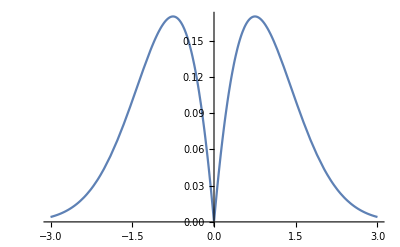

```mathematica
Plot[{Max[0,x]-(1-(CDF[NormalDistribution[x,1]][0])^1)x},{x,-3,3}]
```

```mathematica
D[(1-(CDF[NormalDistribution[]][-x])^n)x,x]==0//FullSimplify
```

1+2^-n (-1+(ⅇ^(-x^2/2) n √(2/π) x)/Erfc[x/(√2)]) Erfc[x/(√2)]^n==0

```mathematica
FindRoot[1+2^-n (-1+(ⅇ^(-x^2/2) n √(2/π) x)/Erfc[x/(√2)]) Erfc[x/(√2)]^n==0/.n->4,{x,-1}]
```

{x→-0.930837}

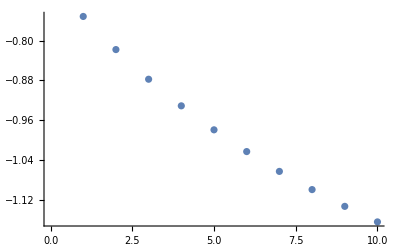

```mathematica
ListPlot[Table[x/.FindRoot[1+2^-n (-1+(ⅇ^(-x^2/2) n √(2/π) x)/Erfc[x/(√2)]) Erfc[x/(√2)]^n==0,{x,-1}],{n,1,10}]]
```

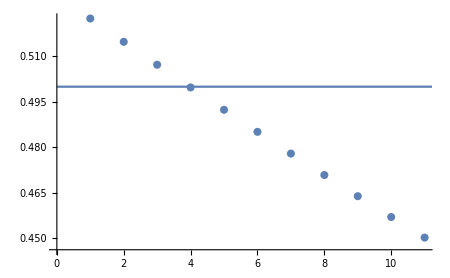

```mathematica
Show[ListPlot[vals[[40;;50]]],Plot[.5,{x,0,300}]]
```

```mathematica
NIntegrate[Max[0,x]-(1-(CDF[NormalDistribution[x,1]][0])^1)x,{x,-Infinity,Infinity}]
```

0.5

```mathematica
vals=Table[NIntegrate[Max[0,x]-(1-(CDF[NormalDistribution[x,1]][a])^5)x,{x,-Infinity,Infinity}],{a,0.,3.,.01}];
```

```mathematica
vals[[115;;120]]
```

{0.224031,0.223851,0.223771,0.223792,0.223912,0.224132}

```mathematica
Table[NIntegrate[Max[0,x]-(1-(CDF[NormalDistribution[x,1]][a])^5)x,{x,-Infinity,Infinity}],{a,1.16,1.18,.005}]
```

{0.223771,0.223769,0.223792,0.223839,0.223912}

```mathematica
NIntegrate[Max[0,x]-(1-(CDF[NormalDistribution[x,1]][.42])^5)x,{x,-Infinity,Infinity}]
```

0.499765